```mathematica
Exit
```

```mathematica
m[r_,l_,Q_] := ((2M r-Q^2)r^3)/(2(r^4+(2M r+Q^2)l^2))/.{M->1}
gtt[r_,l_,Q_,a_,θ_] = -(1-(2m[r,l,Q]r)/(r^2 + a^2 Cos[θ]^2))
```

-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))

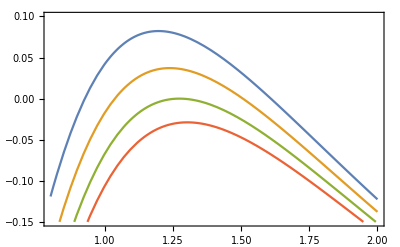

```mathematica
Plot[{gtt[r,0.5,0.2,0.7,Pi/4],gtt[r,0.5,0.2,0.8,Pi/4],gtt[r,0.5,0.2,0.883645,Pi/4],gtt[r,0.5,0.2,0.95,Pi/4]},{r,0.8,2},PlotRange->{{0.8,2},{-0.15,0.1}},Frame->True]
```

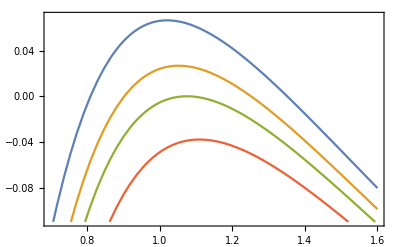

```mathematica
Plot[{gtt[r,0.2,0.82,0.5,Pi/4],gtt[r,0.2,0.85,0.5,Pi/4],gtt[r,0.2,0.8705,0.5,Pi/4],gtt[r,0.2,0.90,0.5,Pi/4]},{r,0.7,1.6},PlotRange->{{0.7,1.6},{-0.11,0.07}},Frame->True]
```

```mathematica
m[r_,l_,Q_] := ((2M r-Q^2)r^3)/(2(r^4+(2M r+Q^2)l^2))/.{M->1}
Σ[r_,a_,θ_] = r^2 + a^2 Cos[θ]^2
Δ[r_,l_,Q_,θ_,a_] = r^2 + a^2 - 2 m[r,l,Q] r
gtt[r_,l_,Q_,a_,θ_] = -(1-(2m[r,l,Q]r)/(r^2 + a^2 Cos[θ]^2))
gtϕ[r_,l_,Q_,a_,θ_]  = -((4a m[r,l,Q])/Σ[r,a,θ])Sin[θ]^2
grr[r_,l_,Q_,θ_,a_] = Σ[r,a,θ]/Δ[r,l,Q,θ,a]
gθθ[r_,a_,θ_] = Σ[r,a,θ]
gϕϕ[r_,l_,Q_,a_,θ_] = (r^2 + a^2 + (2 m[r,l,Q])/Σ[r,a,θ] Sin[θ]^2)Sin[θ]^2
MatrixForm[{{gtt[r,l,Q,a,θ],0,0,gtϕ[r,l,Q,a,θ]},{0,grr[r,l,Q,θ,a],0,0},{0,0,gθθ[r,a,θ],0},{gtϕ[r,l,Q,a,θ],0,0,gϕϕ[r,l,Q,a,θ]}}]
```

r^2+a^2 Cos[θ]^2

a^2+r^2-(r^4 (-Q^2+2 r))/(r^4+l^2 (Q^2+2 r))

-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))

-(2 a r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))

(r^2+a^2 Cos[θ]^2)/(a^2+r^2-(r^4 (-Q^2+2 r))/(r^4+l^2 (Q^2+2 r)))

r^2+a^2 Cos[θ]^2

Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2)))

(-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2)) | 0 | 0 | -(2 a r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))
0 | (r^2+a^2 Cos[θ]^2)/(a^2+r^2-(r^4 (-Q^2+2 r))/(r^4+l^2 (Q^2+2 r))) | 0 | 0
0 | 0 | r^2+a^2 Cos[θ]^2 | 0
-(2 a r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2)) | 0 | 0 | Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))))

```mathematica
a^2+r^2-(r^4 (-Q^2+2 r))/(r^4+l^2 (Q^2+2 r))
```

a^2+r^2-(r^4 (-Q^2+2 r))/(r^4+l^2 (Q^2+2 r))

```mathematica
MatrixForm[Inverse[{{gtt[r,l,Q,a,θ],0,0,gtϕ[r,l,Q,a,θ]},{0,grr[r,l,Q,θ,a],0,0},{0,0,gθθ[r,a,θ],0},{gtϕ[r,l,Q,a,θ],0,0,gϕϕ[r,l,Q,a,θ]}}]]
```

((Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))))/(-(4 a^2 r^6 (-Q^2+2 r)^2 Sin[θ]^4)/((r^4+l^2 (Q^2+2 r))^2 (r^2+a^2 Cos[θ]^2)^2)+(-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))) Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2)))) | 0 | 0 | (2 a r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2) (-(4 a^2 r^6 (-Q^2+2 r)^2 Sin[θ]^4)/((r^4+l^2 (Q^2+2 r))^2 (r^2+a^2 Cos[θ]^2)^2)+(-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))) Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2)))))
0 | (a^2+r^2-(r^4 (-Q^2+2 r))/(r^4+l^2 (Q^2+2 r)))/(r^2+a^2 Cos[θ]^2) | 0 | 0
0 | 0 | 1/(r^2+a^2 Cos[θ]^2) | 0
(2 a r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2) (-(4 a^2 r^6 (-Q^2+2 r)^2 Sin[θ]^4)/((r^4+l^2 (Q^2+2 r))^2 (r^2+a^2 Cos[θ]^2)^2)+(-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))) Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))))) | 0 | 0 | (-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2)))/(-(4 a^2 r^6 (-Q^2+2 r)^2 Sin[θ]^4)/((r^4+l^2 (Q^2+2 r))^2 (r^2+a^2 Cos[θ]^2)^2)+(-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))) Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2)))))

```mathematica
Gtt = (Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))))/
(-(4 a^2 r^6 (-Q^2+2 r)^2 Sin[θ]^4)/((r^4+l^2 (Q^2+2 r))^2 (r^2+a^2 Cos[θ]^2)^2)+(-1+(r^4 (-Q^2+2 r))/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))) Sin[θ]^2 (a^2+r^2+(r^3 (-Q^2+2 r) Sin[θ]^2)/((r^4+l^2 (Q^2+2 r)) (r^2+a^2 Cos[θ]^2))))
```